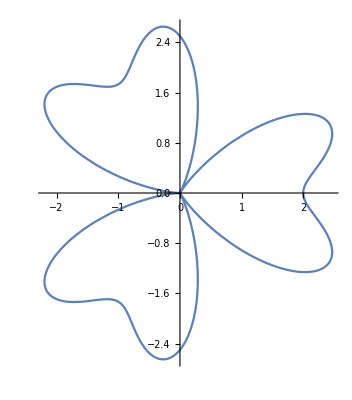

```mathematica
PolarPlot[1+Cos[3 x]+1.5 Sin[3 x]^2,{x,0,2 Pi}]
```

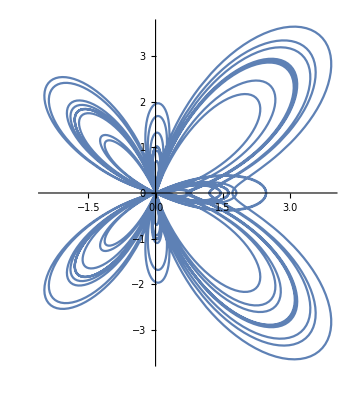

```mathematica
PolarPlot[Exp[Cos[x]]-2 Cos[4 x]+Sin[x/12]^5,{x,0,20 Pi}]
```

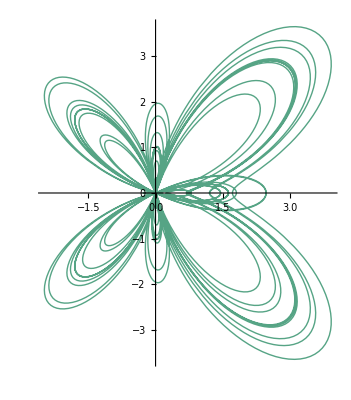

```mathematica
PolarPlot[Exp[Cos[x]]-2 Cos[4 x]+Sin[x/12]^5,{x,0,20 Pi},PlotStyle->Thick,ColorFunction->({x,y}|->Hue[x])]
```

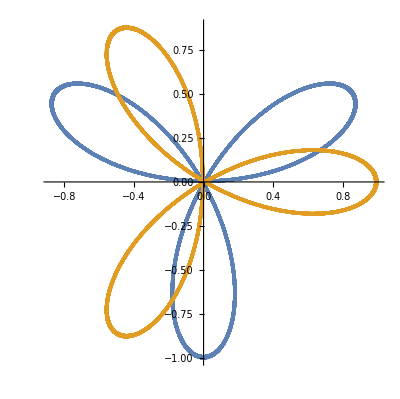

```mathematica
PolarPlot[{Sin[3 x],Cos[3 x]},{x,0,99 Pi}]
```

```mathematica
SphericalPlot3D[Re[Sin[θ]Cos[θ]Exp[2I]],{θ,0,π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Re[Sin[θ]Cos[θ]Exp[2I]],{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Re[Sin[2θ]Cos[2θ]Exp[I]],{θ,0,π},{φ,0,2π}]
```

-Graphics3D-

```mathematica
Manipulate[
ContourPlot[Abs[x]^n+Abs[y]^n==1,{x,-1,1},{y,-1,1}],
{n,1/2,10,1/2}]
```

```mathematica
Manipulate[
ParametricPlot[{Abs[Cos[θ]]^(2/n)Sign[Cos[θ]],Abs[Sin[θ]]^(2/n)Sign[Sin[θ]]},{θ,0,2π}],
{n,0.5,15}]
```

```mathematica
Manipulate[
ParametricPlot[{{Cos[θ]^(2/n) ,Sin[θ]^(2/n)},{-Cos[θ]^(2/n) ,-Sin[θ]^(2/n)},{Cos[θ]^(2/n) ,-Sin[θ]^(2/n)},{-Cos[θ]^(2/n) ,Sin[θ]^(2/n)}},{θ,0,2π}],
{n,0.5,15}]
```